```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
```

```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`InspiralWaves`FourierStrainAmplitude`
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Detector`
```

++ WARNING: PN order convention needs updates!

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

++ To do:
    - fix: does not evolve when |L|<|S| !  
      Need to insure time refinement then  
    - option to DISABLE r evolution (faster DE solutions for long orbits):
       Add DEMO
    - alternate orders, omega(r) forms.  Options to select different orders (no spin/spin; no quad-monopole)
    - SANE END POINT: evolve to final condition
    - PRECESSION PHASE: track it as well...
    - sanity tests (default; interface with NDSolve tools?: prebuilt BinaryPNS) -> check accuracy/stability
    -
    - apply arbitrary rotations to initial data (default positions, orientations)
    - WAVEFORM EXTRACTION: 0th order, + higher harmonics 
    - hamiltonians?  Use HamiltonanODE tools/symplectic integrators
    - rangewrap output, for safety/use
    - document using L as Lnewtonian
    - poincare sections (via EventLocator) : just in 'demo'?

Needs::nocont: Context "MyTools`RangeWrap`" was not created when Needs was evaluated.

Debugme: SPA phase expression: confirm agreement (log terms esp)

+++ Aligned spin: Fix amplitude scaling correctly...

dOperator development: Ok.

DOperator development: Ok.

Get::noopen: Cannot open "Statistics`DataManipulation`".

Needs::nocont: Context "ProgrammingTools`Classes`" was not created when Needs was evaluated.

opts::shdw: Symbol "opts" appears in multiple contexts {"Astrophysics`GravitationalWaves`Detectors`DEPRECATED`", "Global`"}; definitions in context "Astrophysics`GravitationalWaves`Detectors`DEPRECATED`" may shadow or be shadowed by other definitions.

++ WARNING: PN order convention needs updates!

++ To do:
    - fix: does not evolve when |L|<|S| !  
      Need to insure time refinement then  
    - option to DISABLE r evolution (faster DE solutions for long orbits):
       Add DEMO
    - alternate orders, omega(r) forms.  Options to select different orders (no spin/spin; no quad-monopole)
    - SANE END POINT: evolve to final condition
    - PRECESSION PHASE: track it as well...
    - sanity tests (default; interface with NDSolve tools?: prebuilt BinaryPNS) -> check accuracy/stability
    -
    - apply arbitrary rotations to initial data (default positions, orientations)
    - WAVEFORM EXTRACTION: 0th order, + higher harmonics 
    - hamiltonians?  Use HamiltonanODE tools/symplectic integrators
    - rangewrap output, for safety/use
    - document using L as Lnewtonian
    - poincare sections (via EventLocator) : just in 'demo'?

Needs::nocont: Context "MyTools`RangeWrap`" was not created when Needs was evaluated.

Debugme: SPA phase expression: confirm agreement (log terms esp)

+++ Aligned spin: Fix amplitude scaling correctly...

dOperator development: Ok.

DOperator development: Ok.

Get::noopen: Cannot open "Statistics`DataManipulation`".

SetDelayed::write: Tag Class in Class[class_Symbol, superclass_ ? ClassQ, variables : {_Symbol ...}, methods : {{_Symbol, _Function} ...} | {}] is Protected.

TagSet::write: Tag Object in Methods[Object] is Protected.

TagSet::write: Tag Object in InstanceVariables[Object] is Protected.

TagSet::write: Tag Object in SuperClass[Object] is Protected.

General::stop: Further output of TagSet :: write will be suppressed during this calculation.

TagSetDelayed::write: Tag Object in new[Object, init$___] is Protected.

Needs::nocont: Context "ProgrammingTools`Classes`" was not created when Needs was evaluated.

```mathematica
<<PhysicalApplications`Astrophysics`Cosmology`Kinematics`;
```

Cosmology:Kinematics: Warnings : Assumptions inherent in code only apply at relatively low redshifts z<10^9, so T<<m_e

```mathematica
c=3*10^8;(**)
M0=(1.989*10^30 *6.674*10^-11)/c^2;(*Unitless *)
```

```mathematica
F1[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3) UnitStep[1-Mc f/c]
F2[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3)(gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][f, 2^(1/5)Mc/M0, 2^(1/5)Mc/M0,0,0]/gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][10, 2^(1/5)Mc/M0, 2^(1/5)Mc/M0,0,0])
PDFm[Mc_]:=1/Mc^2
F1PDFm[Mc_,f_]:=F1[Mc,f]PDFm[Mc]
F2PDFm[Mc_,f_]:=F2[Mc,f]PDFm[Mc]
```

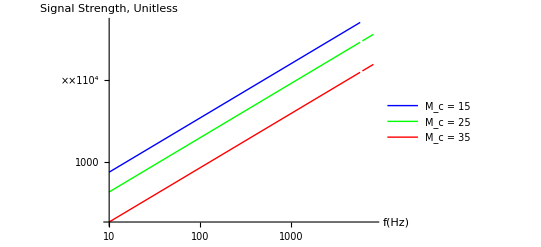

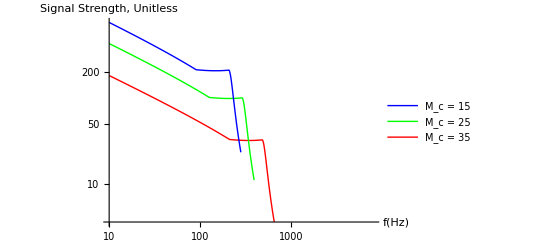

```mathematica
LogLogPlot[{F1[15M0,f],F1[25M0,f],F1[35M0,f]},{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,20],Style["Signal Strength, \n Unitless",Black,Bold,20]},TicksStyle->12,ImageSize->400,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,15],Style["M_c = 25",Black,Bold,15],Style["M_c = 35",Black,Bold,15]}],{0.85,0.35}]]

LogLogPlot[{F2[15M0,f],F2[25M0,f],F2[35M0,f]},{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,20],Style["Signal Strength, \n Unitless",Black,Bold,20]},TicksStyle->12,ImageSize->400,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,15],Style["M_c = 25",Black,Bold,15],Style["M_c = 35",Black,Bold,15]}],{0.6,0.35}]]
```

NIntegrate::inumr: The integrand f^2/3\ UnitStep[1 - f\ Mc/300000000]/100000\ 3^2/3\ 10^1/3\ Mc^1/3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{14749.5, 73747.7}}.

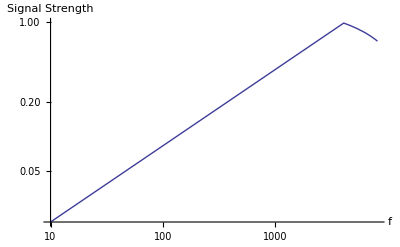

NIntegrate::inumr: The integrand 1.52521×10^-7\ f^2/3\ Which[0.0000983393\ f < 0.0399417, « 6 », 0]/Mc^1/3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{14749.5, 73747.7}}.

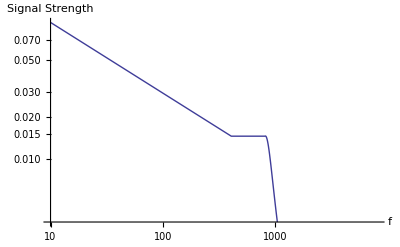

```mathematica
LogLogPlot[NIntegrate[F1PDFm[Mc,f],{Mc,10 M0,50 M0}],{f,10^1,10^3.91},AxesLabel->{Style["f",Black,Bold,15],Style["Signal Strength",Black,Bold,15]},TicksStyle->15]
LogLogPlot[NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}],{f,10^1,10^3.91},AxesLabel->{Style["f",Black,Bold,15],Style["Signal Strength",Black,Bold,15]},TicksStyle->15]
```

```mathematica
?gwFourierStrainModelFunctionPlanarSymmetry
```

gwFourierStrainModelFunctionPlanarSymmetry[Sequence @@ amp] returns a function that specifies the amplitude model provided by 'amp': fn[f,m1,m2].  m1, m2 are numeric in solar masses; f is numeric in seconds.  The source is placed at a distance of 1 Mpc.  In cases where more parameters are possible (e.g., a1,a2, ...) these occur afterwards, in an implementation-dependent order.

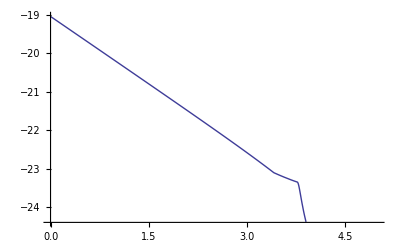

```mathematica
Plot[Log10[gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][10^lf, 1.4, 1.4,0,0]], {lf,0,5}]
```

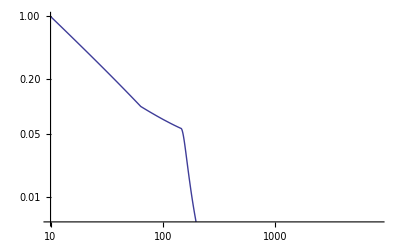

```mathematica
LogLogPlot[gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][f, 2^(1/5)50, 2^(1/5)50,0,0]/gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][10,2^(1/5) 50, 2^(1/5)50,0,0], {f,10^1,10^3.91}]
```

```mathematica
PracticalDistanceLuminosity[z]
```

```mathematica
gwFourierStrainModelFunctionPlanarSymmetryList[]
```

{{NewtonianInspiralOnly,NoTermination},{Phenomenological,IMRPhenomA},{Phenomenological,IMRPhenomB},{InspiralOnly,KerrQNMCutoff,NoRedshifting},{InspiralOnly,SchwarzchildISCO,NoRedshifting},{Phenomenological,AjithAlignedSpinL2,Original,NoRedshifting},{Phenomenological,AjithL2,JenaMatch2,NoRedshifting},{LAL,Nonspinning,model_,paramlist_List}[f_,m1_?NumberQ,m2_?NumberQ]}[]

```mathematica
?gwFourierStrainModelFunctionPlanarSymmetry
```

gwFourierStrainModelFunctionPlanarSymmetry[Sequence @@ amp] returns a function that specifies the amplitude model provided by 'amp': fn[f,m1,m2].  m1, m2 are numeric in solar masses; f is numeric in seconds.  The source is placed at a distance of 1 Mpc.  In cases where more parameters are possible (e.g., a1,a2, ...) these occur afterwards, in an implementation-dependent order.

```mathematica
Solve[M==((m^2)^(3/5))/(2m)^(1/5),m]
```

{{m→-(-2)^(1/5) M},{m→2^(1/5) M},{m→(-1)^(2/5) 2^(1/5) M},{m→-(-1)^(3/5) 2^(1/5) M},{m→(-1)^(4/5) 2^(1/5) M}}